## Question 3

### Part a.

#### The external electric field is given as

```mathematica
Clear["Global *"]
```

```mathematica
Subscript[E, 0][x_,y_,z_]=K{-x,-y,2z}
```

{-K x,-K y,2 K z}

```mathematica
VectorPlot3D[Subscript[E, 0][x,y,z]/.K->1,{x,-3,3},{y,-3,3},{z,-3,3},VectorColorFunction->"DeepSeaColors"]
```

-Graphics3D-

#### In spherical coordinates and components the external electric field is expressed as

```mathematica
Subscript[ER, 0][r_,θ_,ϕ_]=Subscript[E, 0][r Sin[θ] Cos[ϕ],r Sin[θ] Sin[ϕ],r Cos[θ]][[1]]{Sin[θ]Cos[ϕ], Cos[θ]Cos[ϕ],-Sin[ϕ]}+Subscript[E, 0][r Sin[θ] Cos[ϕ],r Sin[θ] Sin[ϕ],r Cos[θ]][[2]]{Sin[θ]Sin[ϕ], Cos[θ]Sin[ϕ],Cos[ϕ]}+
Subscript[E, 0][r Sin[θ] Cos[ϕ],r Sin[θ] Sin[ϕ],r Cos[θ]][[3]]{Cos[θ], -Sin[θ],0}//FullSimplify
```

{1/2 K r (1+3 Cos[2 θ]),-3 K r Cos[θ] Sin[θ],0}

#### Therefore the external potential is

```mathematica
Subscript[Φ, 0][x_,y_,z_]=-Integrate[Subscript[ER, 0][r,θ,ϕ],r]
```

{-1/4 K r^2 (1+3 Cos[2 θ]),3/2 K r^2 Cos[θ] Sin[θ],0}

#### The electric potential solution takes the general form

```mathematica
Subscript[Φ, in][A_,r_,θ_]=A r^2 LegendreP[2,Cos[θ]]
Subscript[Φ, out][C_,r_,θ_]=(C r^-3-K r^2)LegendreP[2,Cos[θ]]
```

1/2 A r^2 (-1+3 Cos[θ]^2)

1/2 (C/r^3-K r^2) (-1+3 Cos[θ]^2)

#### We have the boundary conditions

```mathematica
Subscript[BC, i]=Subscript[Φ, in][A,a,θ]==Subscript[Φ, out][C,a,θ]
Subscript[BC, ii]=(ϵ D[Subscript[Φ, in][A,r,θ],r]/.r->a)==(Subscript[ϵ, 0] D[Subscript[Φ, out][C,r,θ],r]/.r->a)
```

1/2 a^2 A (-1+3 Cos[θ]^2)==1/2 (C/a^3-a^2 K) (-1+3 Cos[θ]^2)

a A ϵ (-1+3 Cos[θ]^2)==1/2 (-(3 C)/a^4-2 a K) (-1+3 Cos[θ]^2) ϵ_0

#### Solve for the coefficients

```mathematica
Coe=Solve[{Subscript[BC, i],Subscript[BC, ii]},{A,C}]//FullSimplify
```

{{A→-(5 K ϵ_0)/(2 ϵ+3 ϵ_0),C→(2 a^5 K (ϵ-ϵ_0))/(2 ϵ+3 ϵ_0)}}

#### So the final expression for the potential is

```mathematica
Subscript[ΦR4, I][r_,θ_]=Subscript[Φ, in][-(5 K Subscript[ϵ, 0])/(2 ϵ+3 Subscript[ϵ, 0]),r,θ]//FullSimplify
Subscript[ΦR4, II][r_,θ_]=Subscript[Φ, out][(2 a^5 K (ϵ-Subscript[ϵ, 0]))/(2 ϵ+3 Subscript[ϵ, 0]),r,θ]//FullSimplify
```

(5 K r^2 (1-3 Cos[θ]^2) ϵ_0)/(4 ϵ+6 ϵ_0)

1/2 (-1+3 Cos[θ]^2) (-K r^2+(2 a^5 K (ϵ-ϵ_0))/(r^3 (2 ϵ+3 ϵ_0)))

#### To plot the field lines, we must first convert the potential to Cartesian coordinates

```mathematica
Subscript[ΦX4, I][x_,y_,z_]=Subscript[ΦR4, I][√(x^2+y^2+z^2),ArcCos[z/(√(x^2+y^2+z^2))]]//FullSimplify
Subscript[ΦX4, II][x_,y_,z_]=Subscript[ΦR4, II][√(x^2+y^2+z^2),ArcCos[z/(√(x^2+y^2+z^2))]]//FullSimplify
```

(5 K (x^2+y^2-2 z^2) ϵ_0)/(4 ϵ+6 ϵ_0)

1/2 (-1+(3 z^2)/(x^2+y^2+z^2)) (-K (x^2+y^2+z^2)+(2 a^5 K (ϵ-ϵ_0))/((x^2+y^2+z^2)^(3/2) (2 ϵ+3 ϵ_0)))

#### Now find the electric field in Cartesian coordinates and components

```mathematica
Subscript[EX4, I][x_,y_,z_]=-Grad[Subscript[ΦX4, I][x,y,z],{x,y,z}]//FullSimplify
Subscript[EX4, II][x_,y_,z_]=-Grad[Subscript[ΦX4, II][x,y,z],{x,y,z}]//FullSimplify
```

{-(5 K x ϵ_0)/(2 ϵ+3 ϵ_0),-(5 K y ϵ_0)/(2 ϵ+3 ϵ_0),(10 K z ϵ_0)/(2 ϵ+3 ϵ_0)}

{(K x (-(3 a^5 (x^2+y^2-4 z^2)+2 (x^2+y^2+z^2)^(7/2)) ϵ+3 (a^5 (x^2+y^2-4 z^2)-(x^2+y^2+z^2)^(7/2)) ϵ_0))/((x^2+y^2+z^2)^(7/2) (2 ϵ+3 ϵ_0)),(K y (-(3 a^5 (x^2+y^2-4 z^2)+2 (x^2+y^2+z^2)^(7/2)) ϵ+3 (a^5 (x^2+y^2-4 z^2)-(x^2+y^2+z^2)^(7/2)) ϵ_0))/((x^2+y^2+z^2)^(7/2) (2 ϵ+3 ϵ_0)),(K z ((4 (x^2+y^2+z^2)^(7/2)+a^5 (-9 (x^2+y^2)+6 z^2)) ϵ+3 (a^5 (3 (x^2+y^2)-2 z^2)+2 (x^2+y^2+z^2)^(7/2)) ϵ_0))/((x^2+y^2+z^2)^(7/2) (2 ϵ+3 ϵ_0))}

#### Finally, we’re ready to plot the field lines inside the sphere

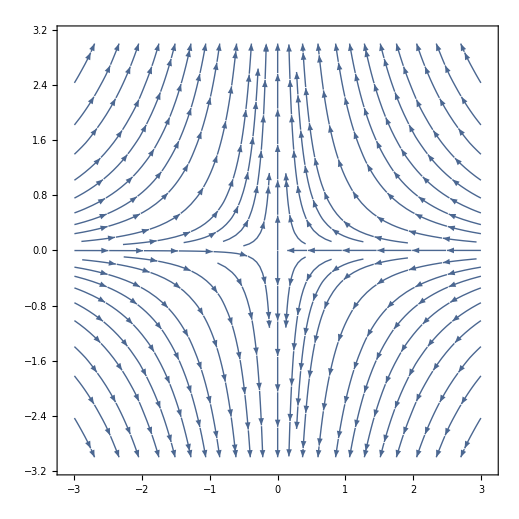

```mathematica
StreamPlot[{Subscript[EX4, I][x,y,z][[1]]/.K-> 1 /.Subscript[ϵ, 0]->1/.ϵ-> 2/.a->1,Subscript[EX4, I][x,y,z][[3]]/.K-> 1 /.Subscript[ϵ, 0]->1/.ϵ-> 2/.a->1},{x,-3,3},{z,-3,3}]
```